```mathematica
$Assumptions=q>0&&q<1&&a>0&&b<0&&λ>0&&Subscript[λ, c]>0
```

q>0&&q<1&&a>0&&b<0&&λ>0&&λ_c>0

```mathematica
Simplify[b/λ-b^2/(4 λ^2)(a/b-(q-1/2)/λ)^2]
```

(b (-b (a/b-(-1/2+q)/λ)^2+4 λ))/(4 λ^2)

```mathematica
Series[(b/λ-b^2/(4 λ^2)(a/b-(q-1/2)/λ)^2)^(1/2),{λ,∞,2}]
```

√b √(1/λ)-(a^2 (1/λ)^(3/2))/(8 √b)+O[1/λ]^(5/2)

```mathematica
Integrate[(b/λ-b^2/(4 λ^2)(a/b-(q-1/2)/λ)^2)^(1/2),{λ,Subscript[λ, c],∞}, PrincipalValue->True]
```

Integrate[√(-(b^2 (a/b-(-1/2+q)/λ)^2)/(4 λ^2)+b/λ),{λ,λ_c,∞},PrincipalValue→True]

```mathematica
ζ=(-a+√(a^2+8b λ))/(4b)
```

(-a+√(a^2+8 b λ))/(4 b)

```mathematica
ρ=(a-2b ζ)/(q-1/2)
```

(a+1/2 (a-√(a^2+8 b λ)))/(-1/2+q)

```mathematica
Simplify[ρ-ρ^2 ζ^2]
```

-((-3 a+√(a^2+8 b λ)) (-a^3-5 a b λ+a^2 √(a^2+8 b λ)+b (b (-2+4 q)+λ √(a^2+8 b λ))))/(2 (b-2 b q)^2)

```mathematica
Clear[ζ]
```

```mathematica
Clear[ρ]
```

```mathematica
Solve[λ==-2b ζ^2+a ζ+(q-1/2)/(a/b-2ζ),ζ]
```

{{ζ→a/(3 b)+(-16 a^2 b^2+96 b^3 λ)/(12 2^(2/3) b^2 (128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ+√(4 (-16 a^2 b^2+96 b^3 λ)^3+(128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ)^2))^(1/3))-((128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ+√(4 (-16 a^2 b^2+96 b^3 λ)^3+(128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ)^2))^(1/3))/(24 2^(1/3) b^2)},{ζ→a/(3 b)-((1+ⅈ √3) (-16 a^2 b^2+96 b^3 λ))/(24 2^(2/3) b^2 (128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ+√(4 (-16 a^2 b^2+96 b^3 λ)^3+(128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ)^2))^(1/3))+((1-ⅈ √3) (128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ+√(4 (-16 a^2 b^2+96 b^3 λ)^3+(128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ)^2))^(1/3))/(48 2^(1/3) b^2)},{ζ→a/(3 b)-((1-ⅈ √3) (-16 a^2 b^2+96 b^3 λ))/(24 2^(2/3) b^2 (128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ+√(4 (-16 a^2 b^2+96 b^3 λ)^3+(128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ)^2))^(1/3))+((1+ⅈ √3) (128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ+√(4 (-16 a^2 b^2+96 b^3 λ)^3+(128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ)^2))^(1/3))/(48 2^(1/3) b^2)}}

```mathematica
ζ=a/(3 b)+(-16 a^2 b^2+96 b^3 λ)/(12 2^(2/3) b^2 (128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ+√(4 (-16 a^2 b^2+96 b^3 λ)^3+(128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ)^2))^(1/3))-((128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ+√(4 (-16 a^2 b^2+96 b^3 λ)^3+(128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ)^2))^(1/3))/(24 2^(1/3) b^2)
```

a/(3 b)+(-16 a^2 b^2+96 b^3 λ)/(12 2^(2/3) b^2 (128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ+√(4 (-16 a^2 b^2+96 b^3 λ)^3+(128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ)^2))^(1/3))-((128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ+√(4 (-16 a^2 b^2+96 b^3 λ)^3+(128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ)^2))^(1/3))/(24 2^(1/3) b^2)

```mathematica
ρ=(a-2b ζ)/(q-1/2)
```

1/(-1/2+q)(a-2 b (a/(3 b)+(-16 a^2 b^2+96 b^3 λ)/(12 2^(2/3) b^2 (128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ+√(4 (-16 a^2 b^2+96 b^3 λ)^3+(128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ)^2))^(1/3))-((128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ+√(4 (-16 a^2 b^2+96 b^3 λ)^3+(128 a^3 b^3-1728 b^5+3456 b^5 q-1152 a b^4 λ)^2))^(1/3))/(24 2^(1/3) b^2)))

```mathematica
Simplify[ρ-ρ^2 ζ^2]
```

-((2 2^(1/3) a^2-12 2^(1/3) b λ+(-4 a^3+36 a b λ-6 b (-9 b+18 b q+√3 √(a^3 (-4+8 q)+36 a b (1-2 q) λ-4 a^2 λ^2+b (27 b (1-2 q)^2+32 λ^3))))^(2/3)-2 a (-2 a^3+18 a b λ-3 b (-9 b+18 b q+√3 √(a^3 (-4+8 q)+36 a b (1-2 q) λ-4 a^2 λ^2+b (27 b (1-2 q)^2+32 λ^3))))^(1/3))^2 (2 2^(1/3) a^2-12 2^(1/3) b λ+(-4 a^3+36 a b λ-6 b (-9 b+18 b q+√3 √(a^3 (-4+8 q)+36 a b (1-2 q) λ-4 a^2 λ^2+b (27 b (1-2 q)^2+32 λ^3))))^(2/3)+4 a (-2 a^3+18 a b λ-3 b (-9 b+18 b q+√3 √(a^3 (-4+8 q)+36 a b (1-2 q) λ-4 a^2 λ^2+b (27 b (1-2 q)^2+32 λ^3))))^(1/3))^2)/(1296 (b-2 b q)^2 (-2 a^3+18 a b λ-3 b (-9 b+18 b q+√3 √(a^3 (-4+8 q)+36 a b (1-2 q) λ-4 a^2 λ^2+b (27 b (1-2 q)^2+32 λ^3))))^(4/3))+1/(-1/2+q)(a-2 b (a/(3 b)+(a^2-6 b λ)/(3 2^(2/3) b (-2 a^3+18 a b λ-3 b (-9 b+18 b q+√3 √(a^3 (-4+8 q)+36 a b (1-2 q) λ-4 a^2 λ^2+b (27 b (1-2 q)^2+32 λ^3))))^(1/3))+((-2 a^3+18 a b λ-3 b (-9 b+18 b q+√3 √(a^3 (-4+8 q)+36 a b (1-2 q) λ-4 a^2 λ^2+b (27 b (1-2 q)^2+32 λ^3))))^(1/3))/(6 2^(1/3) b)))

```mathematica
Series[ρ-ρ^2 ζ^2,{λ,∞,2}]
```

-((-b^3+(b^9)^(1/3))^4 λ^2)/(9 (b^6 (b^9)^(2/3) (-1/2+q)^2))+(4 √(2/3) a (-b^3+(b^9)^(1/3))^3 (b^6+b^3 (b^9)^(1/3)+(b^9)^(2/3)) λ^(3/2))/(9 b^14 (b^9)^(1/6) (-1+2 q)^2)-(2 (a^2 (-b^3+(b^9)^(1/3))^2 (b^6+b^3 (b^9)^(1/3)+(b^9)^(2/3))) λ)/(9 (b^7 (b^9)^(2/3) (-1+2 q)^2))+(2 √(2/3) (-b^3+(b^9)^(1/3)) (b^6+b^3 (b^9)^(1/3)+(b^9)^(2/3)) √λ)/(3 b^7 (b^9)^(1/6) (-1+2 q))+(2 (-a b^6-«1»+2 a («1»)^(«1»)))/(3 («1»)^(2/3) (-1+2 q))+(-(«1»)/(«1»)+«1») «1»+((b^4 (b^3+«1»))/(2 «1»)+(«1»)/(«1»)^2)/λ+(-((-b^3+(b^9)^(1/3)) (a^4-32 a b^2+64 a b^2 q))/(256 √6 b^3 (b^9)^(1/6) (-1/2+q))+(-((-b^3+(b^9)^(1/3)) («8»+48 b^5 («1»)^(«1») q) («1»))/(96 √6 b^4 (b^9)^(5/6))+«12»)/(-1/2+q)^2) (1/λ)^(3/2)+(«1»)/((-1/2+q)^2 λ^2)+O[1/λ]^(5/2)

```mathematica
Clear[ζ]
```

```mathematica
Clear[λ]
```

```mathematica
Clear[ρ]
```

```mathematica
λ[ζ_,a_,b_,q_]=-2b ζ^2+a ζ+(q-1/2)/(a/b-2ζ)
```

(-1/2+q)/(a/b-2 ζ)+a ζ-2 b ζ^2

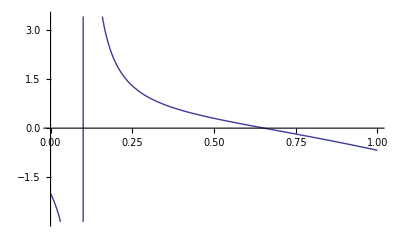

```mathematica
Plot[λ[ζ,0.1,0.5,0.1],{ζ,0,1}]
```